```mathematica
SetDirectory[NotebookDirectory[]];ClearAll["Global`*"];
NotebookEvaluate[AbsoluteFileName["init.nb"]];
MathLink`LinkAddInterruptMessageHandler[$ParentLink];
```

Given a triangle ABC and point X, the Lemoine axis of ABX, BCX, CAX are (sometimes) concurrent on the Lemoine axis of ABC.

The bCoordChangeParam[p, d, e, f] function calculates the barycentric coordinates of a point P wrt some triangle DEF

```mathematica
c1=bCoordChangeParam[{0,-b^2,c^2},xA,xB,pP]//simplifyRationalBarycentrics
```

{c^2 u (u+v+w),c^2 u v+a^2 v w-b^2 w (v+w),c^2 w (u+v+w)}

```mathematica
c2=bCoordChangeParam[{a^2,0,-c^2},xA,xB,pP]//simplifyRationalBarycentrics
```

{c^2 u v+b^2 u w-a^2 w (u+w),c^2 v (u+v+w),c^2 w (u+v+w)}

```mathematica
lc=Cross[c1,c2]//simplifyRationalBarycentrics
```

{-c^2 w (u+v+w) (-a^2 v w+c^2 v (v+w)+b^2 w (v+w)),-c^2 w (u+v+w) (-b^2 u w+c^2 u (u+w)+a^2 w (u+w)),w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^2 u v w (a^2 (u-v+w)+b^2 (-u+v+w))+c^4 u v (u^2+(v+w)^2+u (v+2 w))}

```mathematica
{lc,la,lb}=symtr[lc]
```

{{-c^2 w (u+v+w) (-a^2 v w+c^2 v (v+w)+b^2 w (v+w)),-c^2 w (u+v+w) (-b^2 u w+c^2 u (u+w)+a^2 w (u+w)),w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^2 u v w (a^2 (u-v+w)+b^2 (-u+v+w))+c^4 u v (u^2+(v+w)^2+u (v+2 w))},{u^2 (-c^2 v+b^2 (u+v)) (b^2 w-c^2 (u+w))+a^4 v w (v^2+(u+w)^2+v (2 u+w))+a^2 u v w (b^2 (u+v-w)+c^2 (u-v+w)),-a^2 u (u+v+w) (-b^2 u w+c^2 u (u+w)+a^2 w (u+w)),-a^2 u (-c^2 u v+b^2 u (u+v)+a^2 v (u+v)) (u+v+w)},{-b^2 v (u+v+w) (-a^2 v w+c^2 v (v+w)+b^2 w (v+w)),b^4 u w ((u+v)^2+(u+2 v) w+w^2)+v^2 (c^2 u-a^2 (u+v)) (-a^2 w+c^2 (v+w))+b^2 u v w (a^2 (u+v-w)+c^2 (-u+v+w)),-b^2 v (-c^2 u v+b^2 u (u+v)+a^2 v (u+v)) (u+v+w)}}

bConcurrencyMatrix[] calculates a condition for the concurrency of three lines in barycentric coordinates

```mathematica
fl=bConcurrencyMatrix[la,lb,lc]//FactorList
```

{{1,1},{b^2 u^2+a^2 u v+b^2 u v-c^2 u v+a^2 v^2,1},{-c^2 u^2-a^2 u w+b^2 u w-c^2 u w-a^2 w^2,1},{c^2 v^2-a^2 v w+b^2 v w+c^2 v w+b^2 w^2,1},{c^6 u^4 v^2+c^6 u^3 v^3+c^6 u^2 v^4+2 a^2 b^2 c^2 u^4 v w+b^4 c^2 u^4 v w+b^2 c^4 u^4 v w+a^4 c^2 u^3 v^2 w+6 a^2 b^2 c^2 u^3 v^2 w+2 b^4 c^2 u^3 v^2 w+a^2 c^4 u^3 v^2 w-b^2 c^4 u^3 v^2 w+2 c^6 u^3 v^2 w+2 a^4 c^2 u^2 v^3 w+6 a^2 b^2 c^2 u^2 v^3 w+b^4 c^2 u^2 v^3 w-a^2 c^4 u^2 v^3 w+b^2 c^4 u^2 v^3 w+2 c^6 u^2 v^3 w+a^4 c^2 u v^4 w+2 a^2 b^2 c^2 u v^4 w+a^2 c^4 u v^4 w+b^6 u^4 w^2+a^4 b^2 u^3 v w^2+a^2 b^4 u^3 v w^2+2 b^6 u^3 v w^2+6 a^2 b^2 c^2 u^3 v w^2-b^4 c^2 u^3 v w^2+2 b^2 c^4 u^3 v w^2+a^6 u^2 v^2 w^2+2 a^4 b^2 u^2 v^2 w^2+2 a^2 b^4 u^2 v^2 w^2+b^6 u^2 v^2 w^2+2 a^4 c^2 u^2 v^2 w^2+6 a^2 b^2 c^2 u^2 v^2 w^2+2 b^4 c^2 u^2 v^2 w^2+2 a^2 c^4 u^2 v^2 w^2+2 b^2 c^4 u^2 v^2 w^2+c^6 u^2 v^2 w^2+2 a^6 u v^3 w^2+a^4 b^2 u v^3 w^2+a^2 b^4 u v^3 w^2-a^4 c^2 u v^3 w^2+6 a^2 b^2 c^2 u v^3 w^2+2 a^2 c^4 u v^3 w^2+a^6 v^4 w^2+b^6 u^3 w^3+2 a^4 b^2 u^2 v w^3-a^2 b^4 u^2 v w^3+2 b^6 u^2 v w^3+6 a^2 b^2 c^2 u^2 v w^3+b^4 c^2 u^2 v w^3+b^2 c^4 u^2 v w^3+2 a^6 u v^2 w^3-a^4 b^2 u v^2 w^3+2 a^2 b^4 u v^2 w^3+a^4 c^2 u v^2 w^3+6 a^2 b^2 c^2 u v^2 w^3+a^2 c^4 u v^2 w^3+a^6 v^3 w^3+b^6 u^2 w^4+a^4 b^2 u v w^4+a^2 b^4 u v w^4+2 a^2 b^2 c^2 u v w^4+a^6 v^2 w^4,1}}

checkPointsOnCurve[] checks if any known points in ETC lie on a curve. The curve must be in {u,v,w} or {x,y,z} variables.

```mathematica
checkPointsOnCurve[fl[[5]][[1]]]
```

{}

Given a triangle ABC and point X, the Lemoine axis of ABX, BCX, CAX  form a triangle perspective to ABC. 
If X lies on the circumcircle, the perspector lies on the Lemoine axis of ABC.
If X=X(110) the perspector is at X(512) - infinity point.

bIntersectionTriangle[] is the triangle formed by three given lines.
There are lots of such functions in the repo, like bVertexTriangle, bMidTriangle, bSideTriangle, bCrossTriangle. 
They are all defined in once section of TriangleTools.nb

```mathematica
trg={ia,ib,ic}=simplifyRationalBarycentrics/@bIntersectionTriangle[la,lb,lc]
```

{{a^6 v^2 (u+v) w^2 (u+w)-a^4 u v w (c^2 v+b^2 w) (-u^2+v^2-v w+w^2)-u^2 (c^2 v+b^2 w) (-2 b^2 c^2 u v w+b^4 w (u^2+(v+w)^2+u (2 v+w))+c^4 v (u^2+(v+w)^2+u (v+2 w)))+a^2 u (-2 b^2 c^2 u v w (v^2-v w+w^2+u (v+w))+b^4 w^2 (u^3+w (v+w)^2+u^2 (v+2 w)+u w (5 v+2 w))+c^4 v^2 (u^3+v (v+w)^2+u^2 (2 v+w)+u v (2 v+5 w))),-b^2 v (u+v+w) (w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^4 u v (u^2+u (v+w)+v (v+w))+c^2 w (b^2 u (u^2+u (v+w)+2 v (v+w))+a^2 v (2 u^2+v (v+w)+u (v+2 w)))),-c^2 w (u+v+w) (v^2 (-c^2 u+a^2 (u+v)) (a^2 w-c^2 (v+w))+b^4 u w (u^2+u (v+w)+w (v+w))+b^2 v (c^2 u (u^2+u (v+w)+2 w (v+w))+a^2 w (2 u^2+w (v+w)+u (2 v+w))))},{a^2 u (u+v+w) (w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^4 u v (u^2+u (v+w)+v (v+w))+c^2 w (b^2 u (u^2+u (v+w)+2 v (v+w))+a^2 v (2 u^2+v (v+w)+u (v+2 w)))),-b^6 u^2 (u+v) w^2 (v+w)+b^4 u v w (c^2 u+a^2 w) (u^2-v^2-u w+w^2)+v^2 (c^2 u+a^2 w) (-2 a^2 c^2 u v w+a^4 w (u^2+v^2+v w+w^2+2 u (v+w))+c^4 u (u^2+(v+w)^2+u (v+2 w)))-b^2 v (-2 a^2 c^2 u v w (u^2+u (v-w)+w (v+w))+c^4 u^2 (u^3+2 u^2 (v+w)+v^2 (v+w)+u (2 v^2+5 v w+w^2))+a^4 w^2 (v^3+u^2 w+2 v^2 w+2 v w^2+w^3+u (v^2+5 v w+2 w^2))),c^2 w (u+v+w) (b^4 u^2 (u+v) w+v (c^2 u+a^2 w) (c^2 u (u+w)+a^2 (v^2+v w+w^2+u (v+w)))+b^2 u (-c^2 u (u^2+2 v w+u (v+w))+a^2 w (2 v^2+v w+w^2+u (2 v+w))))},{a^2 u (u+v+w) (v^2 (-c^2 u+a^2 (u+v)) (a^2 w-c^2 (v+w))+b^4 u w (u^2+u (v+w)+w (v+w))+b^2 v (c^2 u (u^2+u (v+w)+2 w (v+w))+a^2 w (2 u^2+w (v+w)+u (2 v+w)))),b^2 v (u+v+w) (b^4 u^2 (u+v) w+v (c^2 u+a^2 w) (c^2 u (u+w)+a^2 (v^2+v w+w^2+u (v+w)))+b^2 u (-c^2 u (u^2+2 v w+u (v+w))+a^2 w (2 v^2+v w+w^2+u (2 v+w)))),-c^6 u^2 v^2 (u+w) (v+w)+c^4 u v (b^2 u+a^2 v) w (u^2-u v+v^2-w^2)+(b^2 u+a^2 v) w^2 (-2 a^2 b^2 u v w+a^4 v (u^2+v^2+v w+w^2+2 u (v+w))+b^4 u (u^2+(v+w)^2+u (2 v+w)))-c^2 w (-2 a^2 b^2 u v w (u^2+u (-v+w)+v (v+w))+a^4 v^2 (u^2 v+v^3+2 v^2 w+2 v w^2+w^3+u (2 v^2+5 v w+w^2))+b^4 u^2 (u^3+2 u^2 (v+w)+w^2 (v+w)+u (v^2+5 v w+2 w^2)))}}

bIsPerspective[] checks if two triangles are perspective. There is also bIsOrthologic[], bIsParallelogic[], and bIsHomothetic[].
triangle[] returns the coordinates of a named triangle. The list of all available triangles is in variable KimberlingTrianglesBary. 
There are other lists of triangles as well: 
CPTR - contains triangles like cevians, pedals, antipedals and many other.
UNCFTRG - unary cofactor triangles of named triangles
ENCTR - Triangles from the Catalog of Central Triangles (https://github.com/lejean2000/Kimberling/blob/main/ctr/README.md)

```mathematica
bIsPerspective[trg, triangle["ABC"]]//Factor
```

0

```mathematica
bParallelogicCenter
```

bTrianglePerspector[] gives the perspector of two triangles if they are perspective. It does not check if they are though. There is also bOrthologyCenter[] and bParallelogicCenter[] which are not symmetric.

```mathematica
bTrianglePerspector[trg, triangle["ABC"]]//simplifyRationalBarycentrics
```

{-a^2 u (v^2 (-c^2 u+a^2 (u+v)) (a^2 w-c^2 (v+w))+b^4 u w (u^2+u (v+w)+w (v+w))+b^2 v (c^2 u (u^2+u (v+w)+2 w (v+w))+a^2 w (2 u^2+w (v+w)+u (2 v+w)))) (w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^4 u v (u^2+u (v+w)+v (v+w))+c^2 w (b^2 u (u^2+u (v+w)+2 v (v+w))+a^2 v (2 u^2+v (v+w)+u (v+2 w)))),-b^2 v (b^4 u^2 (u+v) w+v (c^2 u+a^2 w) (c^2 u (u+w)+a^2 (v^2+v w+w^2+u (v+w)))+b^2 u (-c^2 u (u^2+2 v w+u (v+w))+a^2 w (2 v^2+v w+w^2+u (2 v+w)))) (w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^4 u v (u^2+u (v+w)+v (v+w))+c^2 w (b^2 u (u^2+u (v+w)+2 v (v+w))+a^2 v (2 u^2+v (v+w)+u (v+2 w)))),-c^2 w (b^4 u^2 (u+v) w+v (c^2 u+a^2 w) (c^2 u (u+w)+a^2 (v^2+v w+w^2+u (v+w)))+b^2 u (-c^2 u (u^2+2 v w+u (v+w))+a^2 w (2 v^2+v w+w^2+u (2 v+w)))) (v^2 (-c^2 u+a^2 (u+v)) (a^2 w-c^2 (v+w))+b^4 u w (u^2+u (v+w)+w (v+w))+b^2 v (c^2 u (u^2+u (v+w)+2 w (v+w))+a^2 w (2 u^2+w (v+w)+u (2 v+w))))}

```mathematica
pers=sym3[a^2 u (v^2 (-c^2 u+a^2 (u+v)) (a^2 w-c^2 (v+w))+b^4 u w (u^2+u (v+w)+w (v+w))+b^2 v (c^2 u (u^2+u (v+w)+2 w (v+w))+a^2 w (2 u^2+w (v+w)+u (2 v+w)))) (w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^4 u v (u^2+u (v+w)+v (v+w))+c^2 w (b^2 u (u^2+u (v+w)+2 v (v+w))+a^2 v (2 u^2+v (v+w)+u (v+2 w))))];
```

```mathematica
(* The isogonal conjugate will be simpler, so lets work with it*)
igpers=-simplifyRationalBarycentrics[bIsogonalConjugate[pers]]
```

{v w (b^4 u^2 (u+v) w+v (c^2 u+a^2 w) (c^2 u (u+w)+a^2 (v^2+v w+w^2+u (v+w)))+b^2 u (-c^2 u (u^2+2 v w+u (v+w))+a^2 w (2 v^2+v w+w^2+u (2 v+w)))),u w (v^2 (-c^2 u+a^2 (u+v)) (a^2 w-c^2 (v+w))+b^4 u w (u^2+u (v+w)+w (v+w))+b^2 v (c^2 u (u^2+u (v+w)+2 w (v+w))+a^2 w (2 u^2+w (v+w)+u (2 v+w)))),u v (w^2 (-b^2 u+a^2 (u+w)) (a^2 v-b^2 (v+w))+c^4 u v (u^2+u (v+w)+v (v+w))+c^2 w (b^2 u (u^2+u (v+w)+2 v (v+w))+a^2 v (2 u^2+v (v+w)+u (v+2 w))))}

Given a point which depends on {u,v,w}, massHeuristics1[P, num1, num2] replaces in loop {u,v,w} with X[i] for all i between num1 and num2.
It then checks if the resulting point is in ETC or if it is not in ETC if the expression is simple enough so that it deserves to be checked, usign some heuristics.
Below, you can see that it first prints the list of numbers for which the point is not in ETC but probably simple enough to be worth checking. Second, it prints a list of tuples, e.g. {3, X32002}, which mean that for P=X(3) the expression which we check results in point X(32002).

```mathematica
massHeuristics1[igpers,1,112];
```

{2,6,8,10,23,31,32,36,67,75,76,80}

{{1, X3663}, {3, X32002}, {4, X46724}, {30, X1494}, {74, X1494}, {98, X290}, {99, X670}, {100, X668}, {101, X190}, {102, X34393}, {103, X18025}, {104, X18816}, {105, X2481}, {106, X903}, {107, X6528}, {108, X18026}, {109, X664}, {110, X99}, {111, X671}, {112, X648}}

replacer[Point, num] is a simple function which given a point which depends on {u,v,w}, replaces {u,v,w} with X[num] and simplifies.
replacer[Point, num, num2] works similarly for points which depends on {u,v,w} and {p,q,r}. It replaces {u,v,w} with X[num1] and {p,q,r} with X[num2].

```mathematica
replacer[igpers,2]//simplifyRationalBarycentrics//quickChecker;
```

X(6)X(598)∩X(2)X(5355)

Barycentrics    5*a^4+2*b^4-5*b^2*c^2+2*c^4+7*a^2*(b^2+c^2)

Lies on these lines: {2, 5355}, {4, 33698}, {6, 598}, {32, 32480}, {39, 1153}, {76, 47352}, {83, 5485}, {115, 61046}, {315, 63027}, {316, 8584}, {385, 15810}, {524, 6656}, {538, 66322}, {543, 4027}, {574, 62204}, {597, 11054}, {1992, 7790}, {2482, 63019}, {2549, 52943}, {3329, 14762}, {3849, 39593}, {3972, 11164}, {4045, 44367}, {5007, 19696}, {5008, 9855}, {5032, 5286}, {5041, 33013}, {5305, 63647}, {5306, 26613}, {5309, 8176}, {5319, 7618}, {5346, 33274}, {5461, 63018}, {5476, 38664}, {5976, 7757}, {7606, 13331}, {7617, 7772}, {7619, 7755}, {7620, 32979}, {7739, 8182}, {7753, 41135}, {7754, 21358}, {7765, 19691}, {7769, 41139}, {7797, 41136}, {7801, 7920}, {7803, 21356}, {7806, 64019}, {7817, 7839}, {7828, 41133}, {7840, 7919}, {7841, 7894}, {7856, 34511}, {7876, 63953}, {7877, 33190}, {7878, 34505}, {7905, 8360}, {7924, 63942}, {7937, 15533}, {8352, 20583}, {8369, 63654}, {9465, 52141}, {10159, 60131}, {10336, 11148}, {11163, 14061}, {11185, 63127}, {11286, 63651}, {11648, 12156}, {11842, 12117}, {12203, 19924}, {14035, 53143}, {14482, 23055}, {14568, 16509}, {14614, 55164}, {15048, 51224}, {15484, 62427}, {16044, 53144}, {17503, 54646}, {22329, 63633}, {31168, 41748}, {32971, 43676}, {41895, 45103}, {41940, 47617}, {43448, 63000}, {47286, 63124}, {51185, 60855}, {52229, 66318}, {52713, 54616}, {53106, 54476}, {53109, 60630}, {60143, 63120}, {60279, 60629}, {60282, 60626}, {60628, 60645}, {60638, 62939}

= intersection, other than A, B, C, of circumconics: {{A, B, C, X(10302), X(18818)}}

prmCircumcircle is a t-parametrization of the circumcircle: {a^2/((b-c) (a+(a+b+c) t)),b^2/((-a+c) (b+(a+b+c) t)),c^2/((a-b) (c+(a+b+c) t))}

```mathematica
circ=pers/.Thread[pP->prmCircumcircle]//simplifyRationalBarycentrics
```

{a^2 (b-c) ((b+c) t+a (1+t)),-b^2 (a-c) ((a+c) t+b (1+t)),(a-b) c^2 ((a+b) t+c (1+t))}

massHeuristicsFarey[] is similar to massHeuristics1[] but for points which depend on a real number t. 
The second parameter specifies the set over which t can accept values. fareySet[n] gives all fractions from the Farey Sequence with order at most n, combined with there opposites (e.g. both 1/2 and -1/2 will be part of it).

```mathematica
massHeuristicsFarey[circ,fareySet[10]];
```

{1/10,1/9,1/8,1/7,2/9,2/7,3/10,3/8,2/5,3/7,4/9,5/9,4/7,3/5,5/8,7/10,5/7,7/9,4/5,5/6,6/7,7/8,8/9,9/10,10/9,9/8,8/7,7/6,6/5,5/4,9/7,4/3,7/5,10/7,8/5,5/3,7/4,9/5,9/4,7/3,5/2,8/3,10/3,7/2,9/2,6,7,8,9,10,-1/10,-1/9,-9/10,-10/9,-9/8,-8/7,-9/7,-10/7,-8/5,-9/5,-9/4,-8/3,-10/3,-9/2,-6,-7,-8,-9,-10}

{{1/6, X58136}, {1/5, X58137}, {1/4, X58138}, {1/3, X58139}, {1/2, X58140}, {2/3, X58141}, {3/4, X58142}, {1, X50512}, {3/2, X58143}, {2, X58144}, {3, X58145}, {4, X58146}, {5, X58147}, {-1/8, X58148}, {-1/7, X58149}, {-1/6, X8656}, {-1/5, X58150}, {-2/9, X58151}, {-1/4, X8643}, {-2/7, X58152}, {-3/10, X58153}, {-1/3, X1960}, {-3/8, X58154}, {-2/5, X58155}, {-3/7, X58156}, {-4/9, X58157}, {-1/2, X663}, {-5/9, X58158}, {-4/7, X58159}, {-3/5, X58160}, {-5/8, X58161}, {-2/3, X4775}, {-7/10, X58162}, {-5/7, X58163}, {-3/4, X48338}, {-7/9, X58164}, {-4/5, X58165}, {-5/6, X58166}, {-6/7, X58167}, {-7/8, X58168}, {-8/9, X58169}, {-1, X512}, {-7/6, X58170}, {-6/5, X58171}, {-5/4, X58172}, {-4/3, X58173}, {-7/5, X58174}, {-3/2, X50509}, {-5/3, X58175}, {-7/4, X58176}, {-2, X4834}, {-7/3, X58177}, {-5/2, X58178}, {-3, X58179}, {-7/2, X58180}, {-4, X58181}, {-5, X58182}}

A quick check that shows that for points P on the circumcircle, the perspector which we have been investigating lies on the line X(187)X(237), which has tripole X(6).

```mathematica
{x,y,z}.Cross[X[187],X[237]]/.Thread[{x,y,z}->circ]//Factor
```

0

```mathematica
bTripoleL[Cross[X[187],X[237]]]//quickChecker;
```

ETC: X6

Below we investigate the properties of the triangle formed by the Lemoine axis.

replacerExprNoeval[expr, i] just replaces {u,v,w} with X[i] in expr, without evaluating (i.e. if these is SA, it will stay the same)

trgFullCheck[triangle], performs a series of checks for perspective, orthological, etc. relations to other triangles. It will mention potential homotheties that it finds in red, but this should not be considered a proof. All properties are discoverd numerically.

```mathematica
trg={ia,ib,ic};
```

```mathematica
(*So,this is the triangle for P=X(1)*)
trgchk=simplifyRationalBarycentrics/@replacerExprNoeval[trg,4]
```

{{-a^2 (b-c)^2 (b+c)^2 (a^2-b^2-c^2)^2,b^2 (a^6 (b^2-c^2)+c^2 (-b^2+c^2)^3+a^4 (-2 b^4+b^2 c^2+3 c^4)+a^2 (b^6+b^4 c^2+b^2 c^4-3 c^6)),-c^2 (a^6 (b^2-c^2)-b^2 (b^2-c^2)^3-a^4 (3 b^4+b^2 c^2-2 c^4)+a^2 (3 b^6-b^4 c^2-b^2 c^4-c^6))},{-a^2 (a^6 (b^2-c^2)+c^2 (-b^2+c^2)^3+a^4 (-2 b^4+b^2 c^2+3 c^4)+a^2 (b^6+b^4 c^2+b^2 c^4-3 c^6)),b^2 (a-c)^2 (a+c)^2 (-a^2+b^2-c^2)^2,-c^2 (a^8+b^2 c^2 (b^2-c^2)^2-3 a^6 (b^2+c^2)-a^2 (b^2-c^2)^2 (b^2+c^2)+a^4 (3 b^4+b^2 c^2+3 c^4))},{a^2 (a^6 (b^2-c^2)-b^2 (b^2-c^2)^3-a^4 (3 b^4+b^2 c^2-2 c^4)+a^2 (3 b^6-b^4 c^2-b^2 c^4-c^6)),b^2 (-a^8-b^2 c^2 (b^2-c^2)^2+3 a^6 (b^2+c^2)+a^2 (b^2-c^2)^2 (b^2+c^2)-a^4 (3 b^4+b^2 c^2+3 c^4)),(a-b)^2 (a+b)^2 c^2 (a^2+b^2-c^2)^2}}

Perspector of TR and ABC

Perspector of TR and 4th anti-Euler

X(35709)→{Perspector of TR and anti-Wasat,Perspector of TR and orthic axes}

Perspector of TR and circumcevian of X(24)

Perspector of TR and CTR20-3.4: X1495 - possibly homothetic

Perspector of TR and CTR3-4

X(1495)→{Perspector of TR and CTR20-3.4}

X(11381)→{Perspector of TR and CTR24-69,Perspector of TR and CTR28-69}

Orthology center of TR and {Macbeath}

Orthology center of {Macbeath} and TR

X(11381)→{Orthology center of TR and ABC}

X(5562)→{Orthology center of ABC and TR}

Orthology center of TR and {cevian of X(3), anticevian of X(5), antipedal of X(51), pedal of X(95), cevian of X(97), antipedal of X(184), anticevian of X(216), antipedal of X(217), cevian of X(264), pedal of X(264), pedal of X(276), X(3)-antipedal of X(52), cross-cevian-of-X(2)-and-X(3)}

Orthology center of {anticevian of X(5), antipedal of X(51), cevian of X(68), pedal of X(95), antipedal of X(184), antipedal of X(217), cevian of X(264), pedal of X(264), pedal of X(276), X(1)-circumconcevian of X(9), X(3)-circumconcevian of X(6), X(3)-antipedal of X(52), inverse-of-X(10)-circumconcevian-of-X(37), cross-cevian-of-X(2)-and-X(3)} and TR

X(42441)→{Orthology center of cevian of X(3) and TR}

X(185)→{Orthology center of TR and cevian of X(68)}

X(3)→{Orthology center of cevian of X(97) and TR}

X(52)→{Orthology center of anticevian of X(216) and TR}

X(11381)→{Orthology center of TR and X(1)-circumconcevian of X(9),Orthology center of TR and X(3)-circumconcevian of X(6),Orthology center of TR and inverse-of-X(10)-circumconcevian-of-X(37)}

Orthology center of TR and {CTR7-2.3, CTR7-2.68, CTR10-5, CTR9-2.5, CTR9-3.2, CTR4-3, CTR12-2.95, CTR12-3.54, CTR20-3.4, CTR20-3.5, CTR20-3.68, CTR26-2.2.5}

Orthology center of {CTR7-2.3, CTR7-2.68, CTR10-5, CTR9-2.2, CTR9-2.5, CTR9-3.2, CTR4-3, CTR12-1.2, CTR12-2.95, CTR12-3.54, CTR12-7.2, CTR12-8.2, CTR12-9.2, CTR12-10.2, CTR13-2.2, CTR18-2, CTR20-3.4, CTR3-4, CTR26-2.2.5, CTR26-7.7.65} and TR

X(11381)→{Orthology center of TR and CTR5-2.2,Orthology center of TR and CTR9-2.2,Orthology center of TR and CTR12-1.2,Orthology center of TR and CTR12-7.2,Orthology center of TR and CTR12-8.2,Orthology center of TR and CTR12-9.2,Orthology center of TR and CTR12-10.2,Orthology center of TR and CTR13-2.2,Orthology center of TR and CTR13-32.6,Orthology center of TR and CTR18-2,Orthology center of TR and CTR3-4,Orthology center of TR and CTR26-7.7.65}

X(15043)→{Orthology center of CTR5-2.2 and TR}

X(37488)→{Orthology center of CTR13-32.6 and TR}

X(185)→{Orthology center of CTR20-3.5 and TR}

X(31388)→{Orthology center of CTR20-3.68 and TR}

Parallelogic center of 1st Parry and TR

X(11381)→{Parallelogic center of TR and 1st Parry}

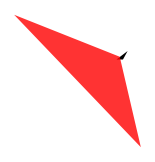

```mathematica
trgFullCheck[trgchk]
```

If a particular calculation leads to a triangle center then this can be considered as a proof. 
For example below we see that our triangle is indeed orthologic to Macbeath.

```mathematica
bOrthologyCenter[triangle["Macbeath"],trgchk]//simplifyRationalBarycentrics//quickChecker;
```

X(5)X(51)∩X(3)X(21638)

Barycentrics    a^2*(-(b^2-c^2)^2+a^2*(b^2+c^2))*(a^8-b^2*c^2*(b^2-c^2)^2-3*a^6*(b^2+c^2)+a^4*(3*b^4+5*b^2*c^2+3*c^4)-a^2*(b^6+b^4*c^2+b^2*c^4+c^6))*(a^6*(b^2+c^2)+3*a^2*(b^2-c^2)^2*(b^2+c^2)-3*a^4*(b^4+c^4)-(b^2-c^2)^2*(b^4+c^4))

Lies on these lines: {3, 21638}, {5, 51}, {185, 32428}, {264, 5889}, {389, 42441}, {511, 26897}, {852, 16625}, {1204, 23709}, {3060, 14249}, {5446, 34334}, {5907, 11197}, {6750, 61195}, {9729, 32078}, {9730, 46025}, {12162, 35719}, {13754, 14978}, {14831, 47301}, {32110, 34292}

= intersection, other than A, B, C, of circumconics: {{A, B, C, X(5), X(389)}}, {{A, B, C, X(343), X(46832)}}